```mathematica
ep=.2;sq[pt_]:=Polygon[{pt-ep,pt+{-ep,ep},pt+ep,pt+{ep,-ep},pt-ep}]
```

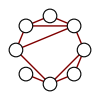
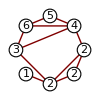

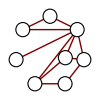
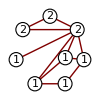

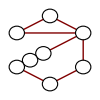
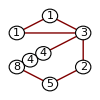

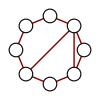
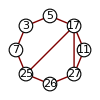

nonplanar-Graphics--Graphics-

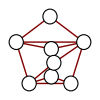
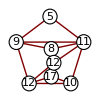

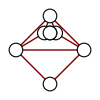
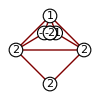

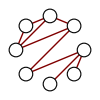
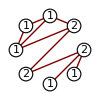

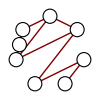
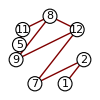

nonplanar-Graphics--Graphics-

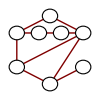
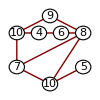

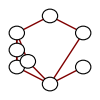
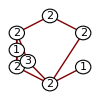

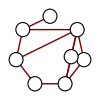
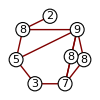

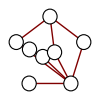
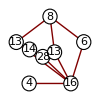

nonplanar-Graphics--Graphics-

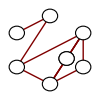
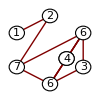

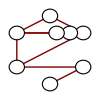
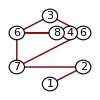

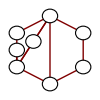
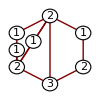

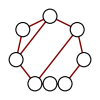
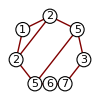

nonplanar-Graphics--Graphics-

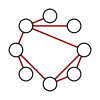
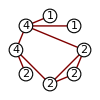

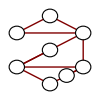
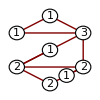

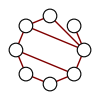
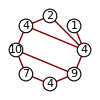

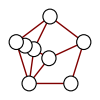
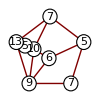

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

«41 more identical outputs»

nonplanar-Graphics--Graphics-

-Graphics--Graphics-

nonplanar-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

«27 more identical outputs»

nonplanar-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

«7 more identical outputs»

nonplanar-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

«3 more identical outputs»

nonplanar-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

«28 more identical outputs»

nonplanar-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

«1 more identical outputs»

nonplanar-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

«19 more identical outputs»

nonplanar-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

nonplanar-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

nonplanar-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

nonplanar-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

nonplanar-Graphics--Graphics-

-Graphics--Graphics-

nonplanar-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

«37 more identical outputs»

nonplanar-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

«15 more identical outputs»

nonplanar-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

«15 more identical outputs»

nonplanar-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

«19 more identical outputs»

```mathematica
num=8;
neigh[n_]:=Complement[Flatten[edges[[Position[edges,n][[All,1]]]]],{n}];
alledges=Select[Tuples[Range[num],2],#[[1]]<#[[2]]&];
For[q=1,q<10000,q++,
edges=Union[RandomChoice[alledges,RandomInteger[{Floor[Binomial[num,2]/3],Binomial[num,2]}]]];
numsol=0;
For[i=1,i≤2^num,i++,
wt=Tuples[{2,4},num][[i]];
s=Solve[Table[wt[[n]]*a[n]==Total[Map[a,neigh[n]]],{n,1,num}]];
If[(a[1]/.s[[1]])=!=0,
values=(({1}~Join~Rest[Array[a,num]])/.s[[1]])/.a[1]->1;
lcm=Apply[LCM,Denominator[values]];
values=values*lcm;
sol=values;numsol++]];If[numsol==1,If[PlanarGraphQ[Graph[edges]],Print[GraphPlot[PlanarGraph[edges],VertexRenderingFunction->({White,EdgeForm[Black],Disk[#,ep]}&),ImageSize->{100,100}],GraphPlot[PlanarGraph[edges],VertexRenderingFunction->({White,EdgeForm[Black],Disk[#,ep],Black,Text[sol[[#2]],#]}&),ImageSize->{100,100}]],Print["nonplanar",GraphPlot[Graph[edges],VertexRenderingFunction->({White,EdgeForm[Black],Disk[#,ep]}&),ImageSize->{100,100}],GraphPlot[Graph[edges],VertexRenderingFunction->({White,EdgeForm[Black],Disk[#,ep],Black,Text[sol[[#2]],#]}&),ImageSize->{100,100}]]]]]
```